## Combi - Example sheet x

Problem 1
a)

```mathematica
Clear[a]
Clear[b]
Clear[c]
a=0.1;
b=1;
c=0.5;
d=1;
dS[S_,P_,k_]:=b(S-P)-c S - (S(P+S))/k-a S P 
dP[S_,P_,k_]:=-c P - (P(P+S))/k+a S P
solution[k_]:=Solve[{dS[s,p,k]==0,dP[s,p,k]==0},{s,p}];
s[k_]:=s/.solution[k]
p[k_]:=p/.solution[k]
s[k]
p[k]
s0=s[30];
p0=p[30];
(*kc/.Solve[{p[kc]==0},kc][[1]]
a=1;
b=2;
c=1.5;
Kmin=b/(a(b-c))-10;
Kmax=b/(a(b-c))+10;
Show[Plot[s[K],{K,Kmin,Kmax}],Plot[p[K],{K,Kmin,Kmax}],PlotRange->All]
```

```mathematica
b)
```

```mathematica
c=2.1;
StreamPlot[{v,-c v -u(1-u)},{u,-0.5,1.5},{v,-1,1}]
ParametricPlot[{v[t], -c v[t] - u[t](1-u[t])},{t,-0.5,1.5}]
```

```mathematica
c)
```

```mathematica
a=0.1;
b=1;
c=0.5;
k=30;
d=1;
L=100;
timeSteps=10000;
S=Table[0,{i,1,100},{j,1,timeSteps}];
P=Table[0,{i,1,100},{j,1,timeSteps}];
S[[50]][[1]]=10;
P[[50]][[1]]=5;
dt=0.01;

For[t=2,t≤timeSteps,t++,For[i=1,i≤L,i++,{S[[i]][[t]]=S[[i]][[t-1]]+(b(S[[i]][[t-1]]+P[[i]][[t-1]])-c S[[i]][[t-1]]-(S[[i]][[t-1]](P[[i]][[t-1]]+S[[i]][[t-1]]))/k-a S[[i]][[t-1]]P[[i]][[t-1]]+d(S[[Mod[(i+1)-1,L]+1]][[t-1]]-2 S[[i]][[t-1]] +S[[Mod[(i-1)-1,L]+1]][[t-1]]))dt,P[[i]][[t]]=P[[i]][[t-1]]+(-c P[[i]][[t-1]]-(P[[i]][[t-1]](P[[i]][[t-1]]+S[[i]][[t-1]]))/k+a S[[i]][[t-1]]P[[i]][[t-1]]+d(P[[Mod[(i+1)-1,L]+1]][[t-1]]-2 P[[i]][[t-1]] +P[[Mod[(i-1)-1,L]+1]][[t-1]]))dt}]]
```

```mathematica
ListDensityPlot[S]
```

```mathematica
ListDensityPlot[P]
```

1.42857

2.69208

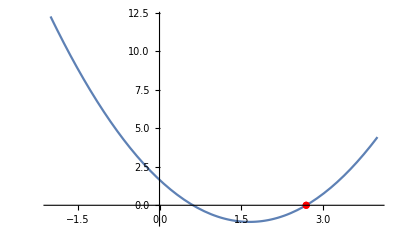

```mathematica
N[5/3.5]
```

Problem 2
a)

```mathematica
s=N[(81+Sqrt[81^2-49*81])/49]
Show[Plot[d^2-162/49 d+81/49,{d,-2,4}],ListPlot[{{s,0}},PlotStyle->Red]]
```

2.69208

```mathematica
b)
```

```mathematica
a=3;
b=8;
L=128;
timeSteps=1000;
d=2.3;
dt=0.01;
u=Table[0,{i,1,L},{j,1,L},{t,1,timeSteps}];
v=Table[0,{i,1,L},{j,1,L},{t,1,timeSteps}];

(*glömt initiering*)
For[t=2, t≤ timeSteps,t++, For[x=1,x≤L,x++,For[y=1,y≤L,y++,{u[[x]][[y]][[t]]=u[[x]][[y]][[t-1]]+(a-(b-1)u[[x]][[y]][[t-1]]+u[[x]][[y]][[t-1]]^2v[[x]][[y]][[t-1]]+u[[Mod[(x+1)-1,L]+1]][[y]][[t-1]]+u[[Mod[(x-1)-1,L]+1]][[y]][[t-1]]+u[[x]][[Mod[(y+1)-1,L]+1]][[t-1]]+u[[x]][[Mod[(y-1)-1,L]+1]][[t-1]]-4u[[x]][[y]][[t-1]])dt, v[[x]][[y]][[t]]=v[[x]][[y]][[t-1]]+(b u[[x]][[y]][[t-1]]-u[[x]][[y]][[t-1]]^2 v[[x]][[y]][[t-1]]+d (v[[Mod[(x+1)-1,L]+1]][[y]][[t-1]]+v[[Mod[(x-1)-1,L]+1]][[y]][[t-1]]+v[[x]][[Mod[(y+1)-1,L]+1]][[t-1]]+v[[x]][[Mod[(y-1)-1,L]+1]][[t-1]]-4v[[x]][[y]][[t-1]]))dt}]]]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

```mathematica
t
```

369